# Fractal Substitution by L-system

## Begin With Edges

Here we only care about edges, even boundary. Maybe later we will consider something about vertex replacement.

This is to generate corresponding really edges, for visualization.

```mathematica
edgeProduce={
e[1|2|5|6|9|10][dir_]:>Sqrt[3]ReIm[Exp[dir*Pi/6 I]],
e[3|4|7|8|11|12|13|14][dir_]:>ReIm[Exp[dir*Pi/6 I]]
};
```

### Replace Rules

Replace a sequence of edges. Obtained by observing factual substitution process.

```mathematica
edgeReplaceRule=
{
{
e[6][dir_],e[7][_:dir_+3],e[8][_:dir_+1],e[9][_:dir_+4],e[10][_:dir_+2],e[11][_:dir_+5]
}:>{
e[4][dir+5],e[5][dir+2],
e[6][dir],e[7][dir+3],e[8][dir+1],e[9][dir+4],e[10][dir+2],e[11][dir+5],
e[12][dir+3],e[13][dir+3],e[14][dir+5],e[1][dir+2]
},
{
e[2][dir_],e[3][_]
}:>{
e[4][dir+5],e[5][dir+2],
e[2][dir],e[3][dir+3],
e[12][dir+1],e[13][dir+1],e[14][dir+3],e[1][dir]
},

{
e[12][dir_],e[13][dir_],e[14][_],e[1][_]
}:>{
e[2][dir-3],e[3][dir],
e[12][dir-2],e[13][dir-2],e[14][dir],e[1][dir-3],
e[2][dir-1],e[3][dir+2],
e[12][dir],e[13][dir],e[14][dir+2],e[1][dir-1],
e[2][dir+1],e[3][dir+4]
},
{
e[4][dir_],e[5][_]
}:>{
e[2][dir-3],e[3][dir],
e[12][dir-2],e[13][dir-2],e[14][dir],e[1][dir-3],
e[2][dir-1],e[3][dir+2]
}
};
```

### Basic Edges

We need some information for one single hat tile. It starts with edge 2, it’s for the convenience of sequence replacing.

```mathematica
basicEdges[dir_:0]:={
e[2][dir+1],
e[3][dir+4],

e[4][dir+6],
e[5][dir+3],

e[6][dir+5],
e[7][dir+8],
e[8][dir+6],
e[9][dir+9],
e[10][dir+7],
e[11][dir+10],

e[12][dir],
e[13][dir],
e[14][dir+2],
e[1][dir-1]
};
```

Pack a function to simplify nest code later.

```mathematica
substitute["e"][edgeList_List]:=Join@@SequenceReplace[edgeList,edgeReplaceRule];
```

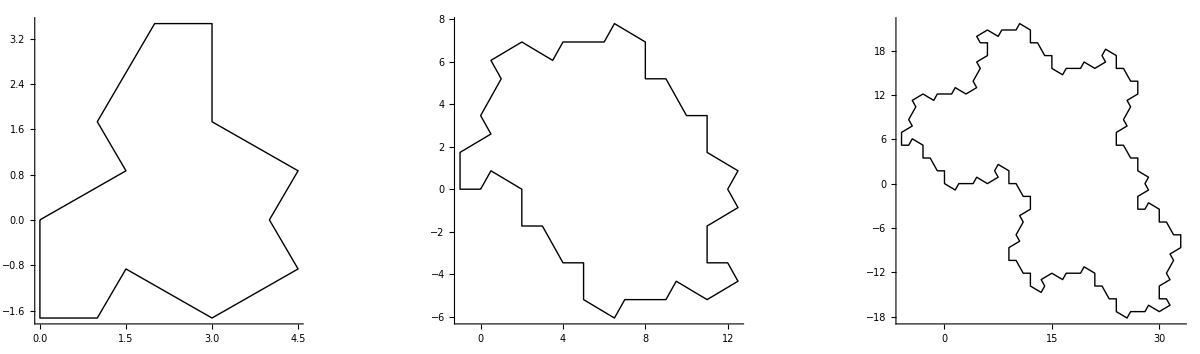

```mathematica
GraphicsRow[
Riffle[
Graphics[Line[#],Axes->True]&/@{
FoldList[Plus,{0,0},basicEdges[8]/.edgeProduce],
FoldList[Plus,{0,0},substitute["e"][basicEdges[8]]/.edgeProduce],
FoldList[Plus,{0,0},Nest[substitute["e"],basicEdges[8],2]/.edgeProduce]
},
Style["→",50,Purple]
]
]
```

It is hard to split list and replace and join every time. Let’s do more analysis:

## More Analysis

There are only 4 replacement rules, here we make them into a table to see clearly.

```mathematica
{Column[#1],Style["→",40],Column[#2]}&@@@edgeReplaceRule//Grid[#,Frame->{False,All},FrameStyle->LightGray,Spacings->{3,5}]&
```

e[6][dir_]
e[7][_:3+dir_]
e[8][_:1+dir_]
e[9][_:4+dir_]
e[10][_:2+dir_]
e[11][_:5+dir_] | → | e[4][5+dir]
e[5][2+dir]
e[6][dir]
e[7][3+dir]
e[8][1+dir]
e[9][4+dir]
e[10][2+dir]
e[11][5+dir]
e[12][3+dir]
e[13][3+dir]
e[14][5+dir]
e[1][2+dir]
e[2][dir_]
e[3][_] | → | e[4][5+dir]
e[5][2+dir]
e[2][dir]
e[3][3+dir]
e[12][1+dir]
e[13][1+dir]
e[14][3+dir]
e[1][dir]
e[12][dir_]
e[13][dir_]
e[14][_]
e[1][_] | → | e[2][-3+dir]
e[3][dir]
e[12][-2+dir]
e[13][-2+dir]
e[14][dir]
e[1][-3+dir]
e[2][-1+dir]
e[3][2+dir]
e[12][dir]
e[13][dir]
e[14][2+dir]
e[1][-1+dir]
e[2][1+dir]
e[3][4+dir]
e[4][dir_]
e[5][_] | → | e[2][-3+dir]
e[3][dir]
e[12][-2+dir]
e[13][-2+dir]
e[14][dir]
e[1][-3+dir]
e[2][-1+dir]
e[3][2+dir]

Notice that there is not any overlap in terms of edge index on the left-hand side, which means we have a partition of edges as:

```mathematica
{
{e[6],e[7],e[8],e[9],e[10],e[11]},
{e[2],e[3]},
{e[12],e[13],e[14],e[1]},
{e[4],e[5]}
}
```

Each group always shows up together and in order, no matter on the left hand side or right hand side.

So, there are only four important equivalent edges, let’s name them:

```mathematica
EToEdges={
E[1][dir_]:>Sequence@@{e[6][dir],e[7][dir+3],e[8][dir+1],e[9][dir+4],e[10][dir+2],e[11][dir+5]},
E[2][dir_]:>Sequence@@{e[2][dir],e[3][dir+3]},
E[3][dir_]:>Sequence@@{e[12][dir],e[13][dir],e[14][dir+2],e[1][dir-1]},
E[4][dir_]:>Sequence@@{e[4][dir],e[5][dir-3]}
};
```

Use E to represent replaceRule:

```mathematica
EReplaceRule={
E[1][dir_]:>{E[4][dir+5],E[1][dir],E[3][dir+3]},
E[2][dir_]:>{E[4][dir+5],E[2][dir],E[3][dir+1]},
E[3][dir_]:>{E[2][dir-3],E[3][dir-2],E[2][dir-1],E[3][dir],E[2][dir+1]},
E[4][dir_]:>{E[2][dir-3],E[3][dir-2],E[2][dir-1]}
};
```

These rules are much simpler. And pack a function for convenience:

```mathematica
substitute["E"][EList_List]:=Join@@ReplaceAll[EList,EReplaceRule];
```

basicE corresponds to basicEdges.

```mathematica
basicE[dir_]:={E[2][dir+1],E[4][dir+6],E[1][dir+5],E[3][dir+0]};
```

Use E to do replacement and generate clusters:

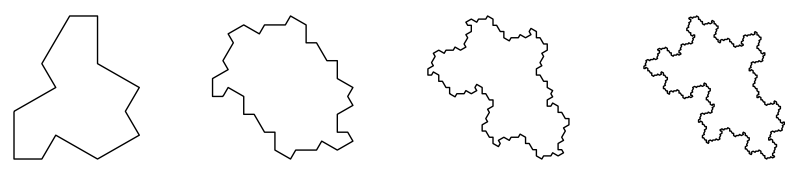

```mathematica
GraphicsRow[
Riffle[
Graphics[Line[
FoldList[
Plus,{0,0},
Nest[substitute["E"],basicE[8],#]/.EToEdges/.edgeProduce
]
]]&/@{0,1,2,3},
Style["→",40,Purple]
],ImageSize->800]
```

## Thinking

The first edges replacement rules are obtained by observation. And we found they can be classified into 4 groups. Then, the substitution rule becomes much simpler represented by these four groups.

Here we draw edges in different groups with different color:

```mathematica
makeColor[E[n_][_]|E[n_]]:=Hue[(n+1)/4]
```

```mathematica
makeColor[E[#]]&/@Range[4]
```

{Hue[Rational[1, 2]],Hue[Rational[3, 4]],Hue[1],Hue[Rational[5, 4]]}

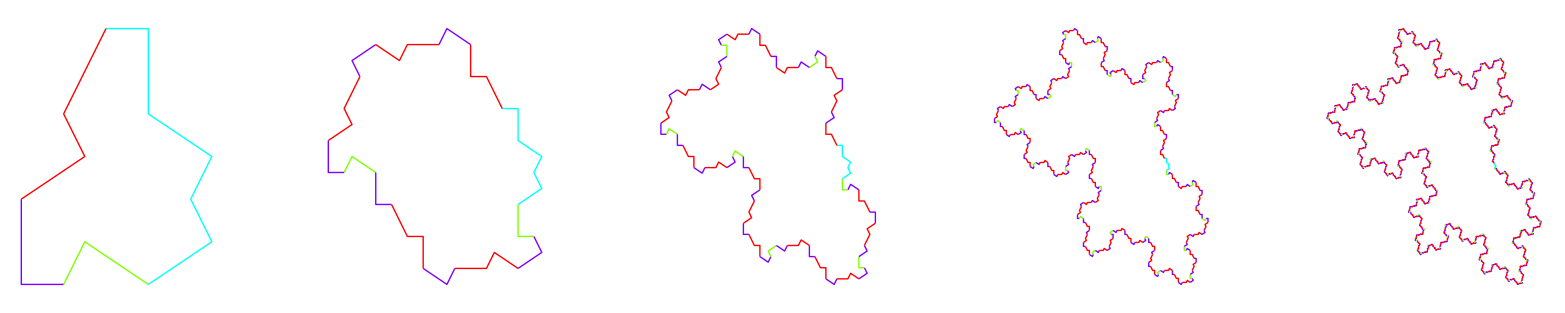

```mathematica
data=Reap[FoldList[
With[{points=FoldList[Plus,#1,{#2/.EToEdges}/.edgeProduce]},
Sow[{makeColor[#2],Line[points]}];
Last[points]
]&,
{0,0},
Nest[substitute["E"],basicE[8],#]
]]&/@{0,1,2,3,4};
GraphicsRow[Riffle[Graphics /@ data[[All,2]], Style["→", 30, Red]], ImageSize -> Full]
```

We notice that, light blue edges only show up in every tiling, and at the same position. According to replacement rule, only E[1] generate E[1] and only one single E[1], so E[1] stay the same all this time.

## Another way to color

Let us try another way to color those edges.

From one single tile, a sequence of edges generate a longer sequence of edges, then color them same. This is how we derive this L-system substitution rule from Figure 2.11 in the original paper. Here let’s show them clearly.

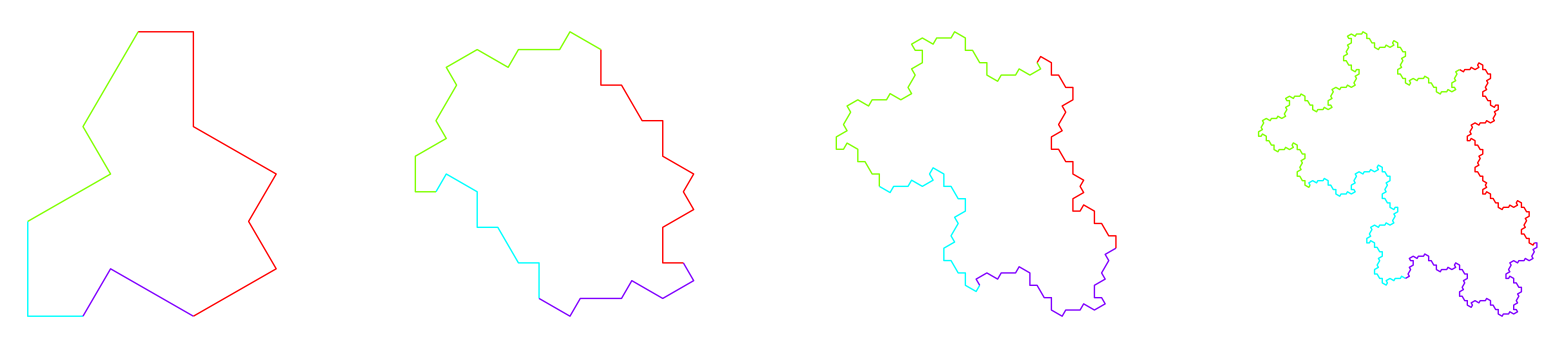

```mathematica
boundarySubstitute=Function[n,Last[Reap[
FoldList[
With[{points=FoldList[Plus,#1,#2[[2]]]},
Sow[{#2[[1]],Thick,Line[points]}];
Last[points]]&,
{0,0},
MapThread[
{makeColor[E[#2]],Flatten[{#1/.EToEdges},n]}&,
{
Nest[substitute["E"][{#}]&,basicE[8],n],
Range[4]
}
]/.edgeProduce
]]]]/@Range[0,3];
GraphicsRow[Riffle[Graphics /@ boundarySubstitute, Style["→", 30, Purple]], ImageSize -> Full]
```

We can see that, there are four segment of edges for each tile. And we notice that there are four important points here. They are the  division points to those four edge sequences.

And it is a little familiar that, these four points are key points we use to generate fractal super-tiles before. Let us review them.

# Substitution rule with 4 control points (By Craig)

This method is by Craig. This is the link: https://gist.github.com/bazzargh/961b6765042b17c0c25eadcc98b080e6

## Depict Tiles

```mathematica
TileVertices[step_][or_,dir_,ref_,pt_] := With[{
basicVertices = AnglePath[{
		{step[[2]], -Pi/6+dir*Pi/6},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[2]], -Pi/2},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], -Pi/3},
		{step[[2]], Pi/2},
		{step[[2]], -Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[1]], 0}
	}]
},
	Expand[# + or&/@(If[ref,{-#[[1]],#[[2]]},#]&/@((#-basicVertices[[pt]])&/@basicVertices))]
]
```

```mathematica
TileEdges[step_][or_,dir_,ref_,pt_] := Partition[TileVertices[step][or,dir,ref,pt], 2, 1, 1]
```

```mathematica
Tile[step_][or_,dir_,ref_,pt_] := Polygon[TileVertices[step][or,dir,ref,pt]]
```

```mathematica
hatVertices:=TileVertices[{1, Sqrt[3]}];
hatEdges:=TileEdges[{1, Sqrt[3]}];
hat:=Tile[{1, Sqrt[3]}];
```

```mathematica
spectreVertices:=TileVertices[{1,1}];
spectreEdges:=TileEdges[{1,1}];
spectre:=Tile[{1,1}];
```

```mathematica
canonicalHat[or_,dir_,ref_,pt_]:={hatVertices[or,dir,ref,pt][[1]], dir, ref, 1}
```

## Visualization

```mathematica
Options[depictControlPoints]=Join[Options[Graphics],Options[Show],{step->{1,1},chooseColor->{Blue,Yellow}}];
depictControlPoints[tile_,opt:OptionsPattern[]]:=
Graphics[
{
EdgeForm[Purple],
tile["tiles"],
Red,PointSize[.03],
Point[tile["controlPoints"]],
Line[Partition[tile["controlPoints"],2,1,1]]
},
opt
];
```

## Manipulate Cluster

```mathematica
rotateCluster[tiles_,r_]:=tiles/.p_Polygon:>RotationTransform[r*Pi/6][p]

translateCluster[tiles_,vec_]:=tiles/.p_Polygon:>TranslationTransform[vec][p]

placeCluster[pos_,dir_,tiles_]:=translateCluster[rotateCluster[tiles,dir],pos];
```

```mathematica
rotateTiling[tiling_, r_] := <|
	"tiles" -> rotateCluster[tiling["tiles"], r],
	"controlPoints" -> (Expand[RotationMatrix[r * Pi/6] . #] & /@ tiling["controlPoints"])
|>

translateTiling[tiling_, vec_] := <|
	"tiles" -> translateCluster[tiling["tiles"], vec],
	"controlPoints" -> (Expand[# + vec] & /@ tiling["controlPoints"])
|>

placeTiling[pos_, dir_, code_] := translateTiling[rotateTiling[code, dir], pos];
```

```mathematica
reflectCode[tiles_]:=tiles/.p_Polygon:>ReflectionTransform[{1,0}][p]
reflectTiling[tiling_] := <|"tiles"->reflectCode[tiling["tiles"]],"controlPoints"->Apply[{-#1,#2}&,tiling["controlPoints"],1]|>
```

### hat rule works for hat only

```mathematica
substitute["hat"][tiling1_,tiling2_]:=With[
{
t1=placeTiling[-tiling1["controlPoints"][[1]],0,tiling1],
t2=placeTiling[-tiling2["controlPoints"][[1]],0,tiling2]
},
Module[
{
T1,T2,T3,T4,T5,T6,T7,T8
},
T1=t2;
T2=placeTiling[T1["controlPoints"][[4]]-RotationMatrix[10Pi/6].t2["controlPoints"][[2]],10,t2];
T3=placeTiling[T2["controlPoints"][[4]]-RotationMatrix[8Pi/6].t2["controlPoints"][[2]],8,t2];
T4=placeTiling[T3["controlPoints"][[3]],8,t2];
T5=placeTiling[T4["controlPoints"][[4]]-RotationMatrix[6Pi/6].t2["controlPoints"][[2]],6,t2];
T6=placeTiling[T5["controlPoints"][[4]]-RotationMatrix[4Pi/6].t2["controlPoints"][[2]],4,t2];
T7=placeTiling[T6["controlPoints"][[4]]-RotationMatrix[8Pi/6].t2["controlPoints"][[4]],8,t1];

Sow[{T1,T2,T3,T4,T5,T6,T7}];

<|
"tiling1"->placeTiling[tiling1["controlPoints"][[1]],0,
<|
"tiles"->Join@@(#["tiles"]&/@{T1,T2,T3,T5,T6,T7}),
"controlPoints"->{
T1["controlPoints"][[2]],
T2["controlPoints"][[3]],
T4["controlPoints"][[2]],
T6["controlPoints"][[3]]
}
|>
],
<|
"tiling2"->placeTiling[tiling1["controlPoints"][[1]],0,
<|
"tiles"->Join@@(#["tiles"]&/@{T1,T2,T3,T4,T5,T6,T7}),
"controlPoints"->{
T1["controlPoints"][[2]],
T2["controlPoints"][[3]],
T4["controlPoints"][[2]],
T6["controlPoints"][[3]]
}
|>
]
|>
|>

]
]
```

## Tile Information

```mathematica
H1Tiling=<|
"tiles"->{{LightBlue,Opacity[.8],EdgeForm[Black],Tile[{1,Sqrt[3]}]@@{{0,0},8,False,6}}},
"controlPoints"->(TileVertices[{1,Sqrt[3]}]@@{{0,0},8,False,6})[[{6,4,2,12}]]
|>;
H2Tiling=<|"tiles"->
{
{Lighter@Blue,Opacity[.7],Tile[{1,Sqrt[3]}]@@{{0,0},8,False,6}},
{Darker@Blue,Opacity[.8],Tile[{1,Sqrt[3]}]@@{(TileVertices[{1,Sqrt[3]}]@@{{0,0},8,False,6})[[1]],2,True,9}}
},
"controlPoints"->(TileVertices[{1,Sqrt[3]}]@@{{0,0},8,False,6})[[{6,4,2,12}]]
|>;
```

## Fractal Substitution

```mathematica
res=NestList[Values[substitute["hat"][#[[1]],#[[2]]]]&,{H2Tiling,H1Tiling},3];
```

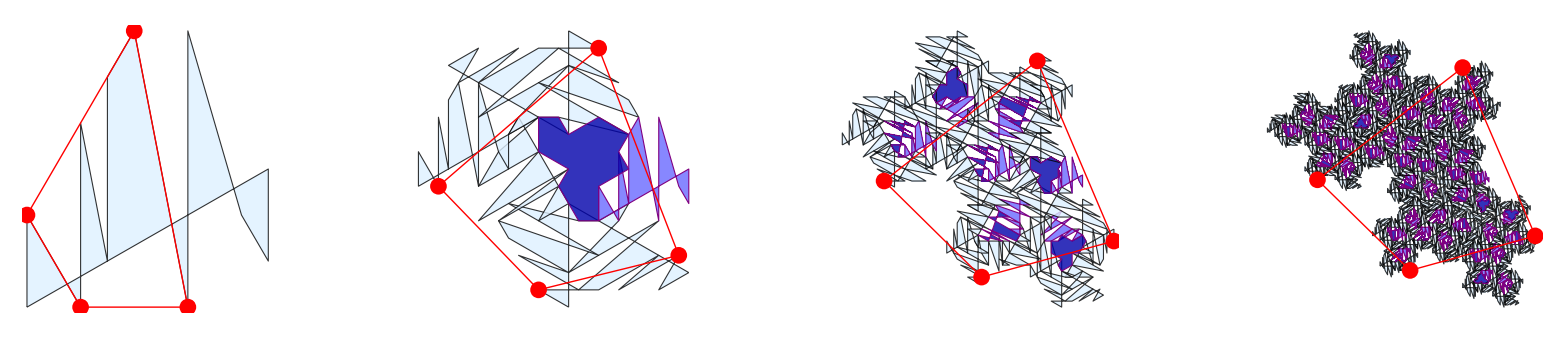

```mathematica
Riffle[
MapThread[
depictControlPoints[rotateTiling[#1,#2]]&,
{
res[[All,2]],
{0,4,8,0}
}],
Style["→",Purple,40]
]//GraphicsRow[#,ImageSize->Full]&
```

## Comparison

For comparison, we overlap two figures in different orders in Show. Because the order influent how it is shown.

We can see that, each key point is a division to two edge sequence.

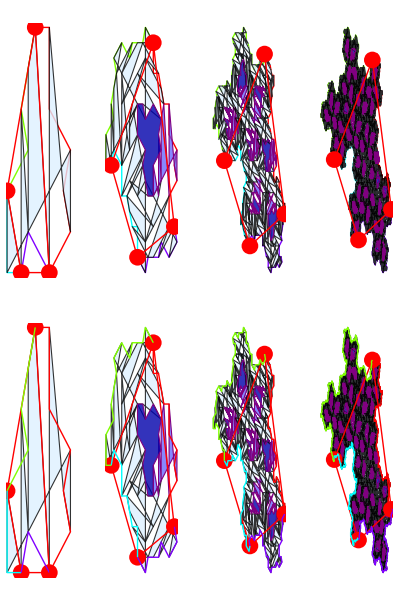

```mathematica
With[{
g1=GraphicsRow[Riffle[Graphics /@ boundarySubstitute, Style["→", 30, Purple]], ImageSize -> Full],
g2=GraphicsRow[
Riffle[
MapThread[
depictControlPoints[rotateTiling[#1,#2]]&,
{
res[[All,2]],
{0,4,8,0}
}],
Style["→",Purple,30]
],ImageSize->Full]
},
{Show[g1,g2],Show[g2,g1]}//Column
]
```